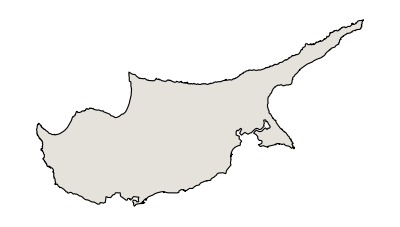
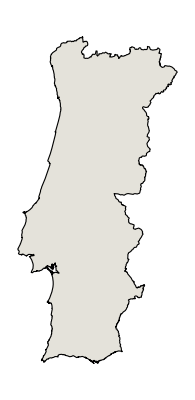
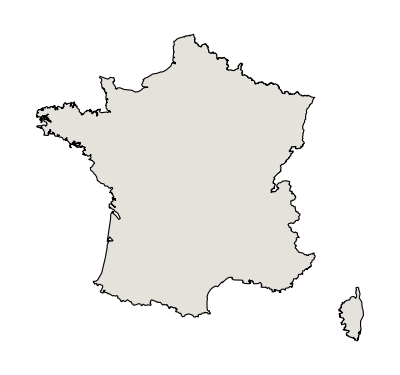
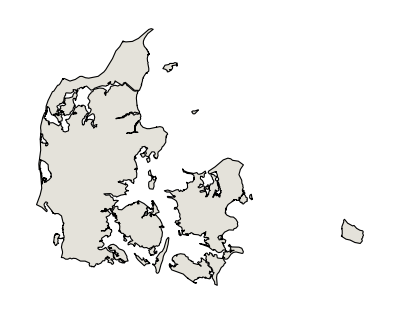
{{Cyprus,124.679 people/km^2,-Graphics-},{Portugal,116.248 people/km^2,-Graphics-},{France,116.231 people/km^2,-Graphics-},{Denmark,130.62 people/km^2,-Graphics-}}

```mathematica
Map[{#[[1]],CountryData[#[[1]],"Population"]/CountryData[#[[1]],"Area"],CountryData[#[[1]],"Shape"]}&,SortBy[{#,Abs[CountryData["Poland","Population"]/CountryData["Poland","Area"]-CountryData[#,"Population"]/CountryData[#,"Area"]]}&/@CountryData["EU"],Last][[2;;5]]]
```